Количество абонентов, имеющих удовлетворительное качество связи: 60538420

Количество количество всех людей: 93510850

Процентное соотношение удавлетворенных абонентов: 64.7395%

-Graphics3D-

-Graphics3D-

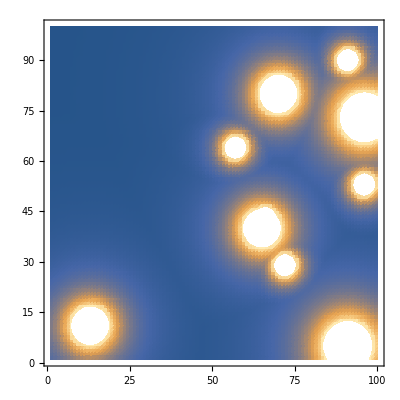

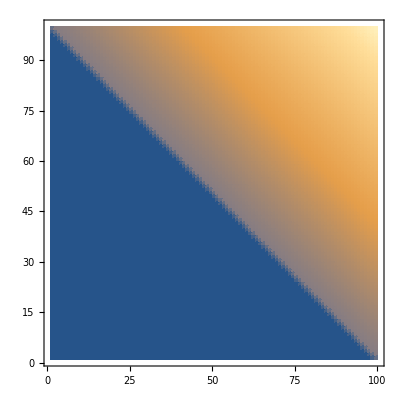

Plot3D::argr: Plot3D called with 1 argument; 3 arguments are expected.

Plot3D[finalMap,PlotRange→All]

Plot3D::argr: Plot3D called with 1 argument; 3 arguments are expected.

Plot3D[humans,PlotRange→All]

```mathematica
humans=Table[Table[0,{100}],{100}];
For [ i=1, i≤100, i++,
For[j= 100 - i +1, j≤ 100  , j++,
humans[[i,j]]=(i+j)^2;
];
];

towers = List[];  
finalMap =Table[Table[0,{100}],{100}];
SetTower[power_, number_] := Module[{pow = power, num = number},
For[i=0,i<num, i++,   
met = True;
While[met == True,
met=False;
x = RandomInteger[{1, 100}];
y = RandomInteger[{1, 100}];
For[j=1,j≤Length[towers],j++,
If[towers[[j,1]]==x && towers[[j,2]]==y,met = True];
];
];
point = List[x,y,pow];
AppendTo[towers, point];
];
];

SetTower[100,5];
SetTower[300,3];
SetTower[500,2];

For[i=1,i≤100,i++, 
For[j=1,j≤100,j++,
For[k=1, k≤Length[towers],k++,
x = towers[[k,1]];
y=towers[[k,2]];
If[x==i && y==j,
finalMap[[i,j]] = towers[[k, 3]];
Continue[];
];
d2 =  (i - x)^2 + (j - y)^2 ;
power =  towers[[k,3]] / d2;
If[power>finalMap[[i,j]], finalMap[[i,j]]=power];
];
];
];
countHumans=0;
allHumans = 0;      
For[i=1,i≤100,i++,
For[j=1,j≤100,j++,
allHumans+= humans[[i,j]];
If[finalMap[[i,j]] > 1,
countHumans+= humans[[i,j]];];
];
];
Print["Количество абонентов, имеющих удовлетворительное качество связи: ",countHumans];
Print["Количество количество всех людей: ",allHumans];
Print["Процентное соотношение удавлетворенных абонентов: ",N[countHumans/allHumans * 100], "%"];
ListPlot3D[finalMap,PlotRange->All]
ListPlot3D[humans,PlotRange->All]


ListDensityPlot[finalMap]
ListDensityPlot[humans]
(* ListPlot3D[finalMap] *)

Plot3D[finalMap,PlotRange->All]
Plot3D[humans,PlotRange->All]
```